# Retrospective evaluation of school-related measures on pre-vaccination dynamics of SARS-CoV-2

## Canfora B., Escosio R. A., Boldea O., van Dorp C. H., Nunes A., and Rozhnova G.

## Memory and global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### PACKAGES AND PARAMETERS

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plottingFunctions`"];

(*ResourceFunction["DarkMode"][False]*)
(*ResourceFunction["GraphicsBrace"];*)


(* Notebook parameters *)
ifShowFigs = True;
ifExportData = True;
ifExportFigs = True;
exportFormat={".pdf",".eps"};

importExportScenarioResults[labelPrefix_,dataFunction_, subFolder_]:=
Table[Module[{filePath,state},
filePath=FileNameJoin[{"../results"},StringJoin["/",subFolder,"/",labelPrefix,"_",scenarios[[i]],".wxf"]];
If[FileExistsQ[filePath],
state=Import[filePath,"WXF"];
state,
state=dataFunction[i];
Export[filePath,state,"WXF","CompressionLevel"->5];
state]],
{i,1,Length[scenarios]}];

exportFigs[figs_, filename_] := If[ifExportFigs,Table[Export[StringJoin["../figures/",filename, ToString[j],exportFormat⟦i⟧],figs⟦j⟧],{i,1,Length[exportFormat]},{j,1,Length[figs]}]];


(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;

(* Scenarios *)
(*scenarios={"Baseline", "Scenario1", "Scenario2", "Scenario1_RelaxedNS", "Scenario1_ZetaSchool","Scenario2_ZetaZetaS", "Scenario2_RelativeSchool"};*)
scenarios={"Baseline", "Scenario1", "Scenario2"};
numScenarios = Length[scenarios];
```

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

### IMPORTANT DATES AND TIME STEP

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)

(* Date of 2020 school vacation : June 10, 2020 *)
timeSchoolVacation=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 06, 10}]}]⟦1,1⟧+1;

(* Integration end-time and time step *)
(*Subscript[t, step]=1;
Subscript[t, end]=timeEndData;
Subscript[t, start]=timeStart;
times =Range[Subscript[t, start],Subscript[t, end],Subscript[t, step]];
numTimes = Length[times];*)
(* Scenario time points *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(*(* Scenario time points *)
Subscript[t, start,1]="February 25, 2020";
Subscript[t, end,1]="July 15, 2020";
Subscript[t, start,2]="July 15, 2020";
Subscript[t, end,2]="January 16, 2021";*)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### CONTACT MATRICES FROM VESPIGNANI ET AL.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
schoolContactsMultiplier = 11.41;
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolRawContactDataBefore85=  Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];
schoolContactDataBefore85 = schoolContactsMultiplier * schoolRawContactDataBefore85;


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
calculateContactsAgeGroups2=calculateTotalContsPerPar[contactDataBefore85, 85];
calculateSchoolContactsAgeGroups2=calculateTotalContsPerPar[schoolContactDataBefore85, 85];
```

### TRANSFORMING THE CONTACT MATRICES FROM 86x86 TO 10x10

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

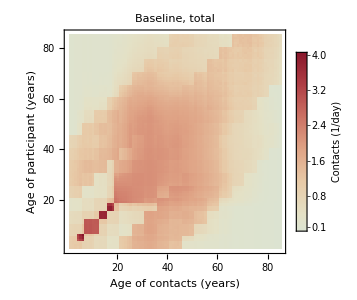
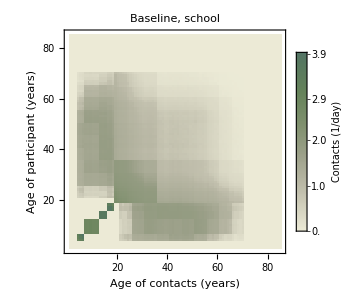
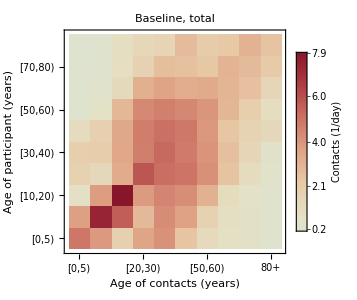
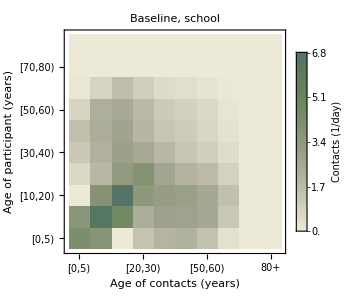
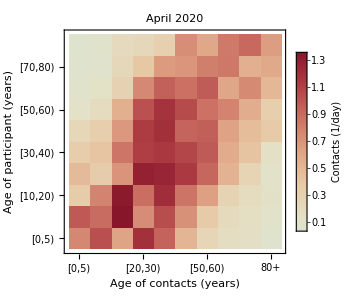
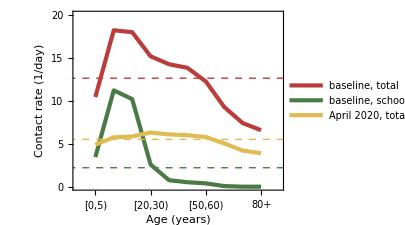
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];

contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];


(* Assigning parameter variables *)
contactRates:=
Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10⟦k,l⟧,Subscript[a,{k,l}]->contactDataAfter10⟦k,l⟧,
Subscript[s, {k, l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];


(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];


(* Plotting *)
figTotalConmat = plotMatrix[contactDataBefore85, "ThermometerColors" ,"Baseline, total", "contact", ImagePadding->{{70, 0}, {Automatic,0}}];
figSchoolConmat = plotMatrix[schoolContactDataBefore85, ColorData[{"AlpineColors", {1.15,0.45}}] ,"Baseline, school","contact", ImagePadding->{{70, 0}, {Automatic,0}}];
figContactMatrixBefore = plotMatrix[contactDataBefore10, "ThermometerColors" ,"Baseline, total", "contact"];
figSchoolContactMatrixBefore = plotMatrix[schoolContactDataBefore10, ColorData[{"AlpineColors", {1.15,0.45}}] ,"Baseline, school","contact"];
figContactMatrixAfter = plotMatrix[contactDataAfter10, "ThermometerColors", "April 2020", "contact"];
figTotalContPerAge =
plotThickLine[{calculateContactsAgeGroupsBefore, 
calculateSchoolContactsAgeGroupsBefore,
calculateContactsAgeGroupsAfter},{colorDarkRed, colorDarkGreen, colorYellow},"","Age (years)","Contact rate (1/day)",{"baseline, total", "baseline, schools", "April 2020, total"},
"contacts",
{calculateAverageContactRateBefore, calculateAverageContactRateSchoolsBefore, calculateAverageContactRateAfter}, 
{{0, 11}, {0, 20}}, 
ImagePadding->{{40, Automatic}, {Automatic, Automatic}}] ;

Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figContsA = plotWithLetter[figTotalConmat, "A"];
figContsB = plotWithLetter[figSchoolConmat, "B"];
figContsC = plotWithLetter[figContactMatrixBefore, "C"];
figContsD = plotWithLetter[figSchoolContactMatrixBefore, "D"];
figContsE = plotWithLetter[figContactMatrixAfter, "E"];
figContsF = plotWithLetter[figTotalContPerAge, "F"];
figConts = Grid[{{figContsA, figContsB}, {figContsC, figContsD}, {figContsE, figContsF}}];
If[ifShowFigs, figConts]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS",  exportFormat[[i]]],figConts], {i, 1, Length[exportFormat]}]];
```

## Hospitalization data and estimated parameters

### ESTIMATED PARAMETERS

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];


(* Assigning parameters *)
probabOfTransmEpsilon[sample_]:=ϵ->estimatesData⟦sample,1⟧;
probabOfTransmZeta[sample_]:=ζ-> estimatesData⟦sample,2⟧;
hospitalizationRate[sample_]:=Table[Subscript[ν,k]->estimatesData⟦sample,2+k⟧,{k,1,numAgeGroups}];
susceptibility[sample_]:=Flatten[Join[
Table[Subscript[β,k]->estimatesData⟦sample,14⟧ ,{k,1,3}],
Table[Subscript[β,k]->estimatesData⟦sample,15⟧ ,{k,4,7}],
Table[Subscript[β,k]->estimatesData⟦sample,16⟧ ,{k,8,10}]]];
latencyRate[sample_]:=α->estimatesData⟦sample,18⟧;
recoveryRate[sample_]:=γ->estimatesData⟦sample,19⟧;
rOverDisp[sample_]:=estimatesData⟦sample,17⟧;
logFuncParams[sample_]:={Subscript[xx, 0]-> estimatesData⟦sample,20⟧,Subscript[K, 0]-> estimatesData⟦sample,21⟧,Subscript[xx, 1]-> estimatesData⟦sample,22⟧,Subscript[K, 1]-> estimatesData⟦sample,23⟧,Subscript[xx, 2]-> estimatesData⟦sample,24⟧,Subscript[K, 2]-> estimatesData⟦sample,25⟧,Subscript[xx, 3]-> estimatesData⟦sample,26⟧,Subscript[K, 3]-> estimatesData⟦sample,27⟧,Subscript[xx, 4]-> estimatesData⟦sample,28⟧,Subscript[K, 4]-> estimatesData⟦sample,29⟧};
uParams[sample_]:={Subscript[u, 1]-> estimatesData⟦sample,30⟧,Subscript[u, 2]-> estimatesData⟦sample,31⟧,Subscript[u, 3]-> estimatesData⟦sample,32⟧,Subscript[u, 4]-> estimatesData⟦sample,33⟧} ;
totalPop:=Table[Subscript[NN,k]-> demographyData10⟦k⟧,{k,listAgeGroups}];
initConds[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-estimatesData⟦sample,13⟧,Subscript[EE0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[II0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,listAgeGroups}]];


(* Table for all parameters *)
parameters[sample_]:=
Flatten[{contactRates,totalPop,probabOfTransmEpsilon[sample],probabOfTransmZeta[sample],hospitalizationRate[sample],initConds[sample],susceptibility[sample],logFuncParams[sample],uParams[sample],latencyRate[sample],recoveryRate[sample]}];

(* Table of parameters with just the values *)parameterConstVals = {estimatesData⟦All,1⟧ 100,estimatesData⟦All,2⟧,estimatesData⟦All,13⟧ Total[demographyData10],estimatesData⟦All,14⟧,estimatesData⟦All,15⟧,estimatesData⟦All,17⟧,1/estimatesData⟦All,18⟧,1/estimatesData⟦All,19⟧};
parameterTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧,estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
parameterKVals = {estimatesData⟦All,21⟧,estimatesData⟦All,23⟧,estimatesData⟦All,25⟧,estimatesData⟦All,27⟧,estimatesData⟦All,29⟧};
parameterUVals = {estimatesData⟦All,30⟧,estimatesData⟦All,31⟧,estimatesData⟦All,32⟧,estimatesData⟦All,33⟧};
parameterHospRateVals = Table[365 estimatesData⟦All,2+i⟧,{i,1,numAgeGroups}];
```

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

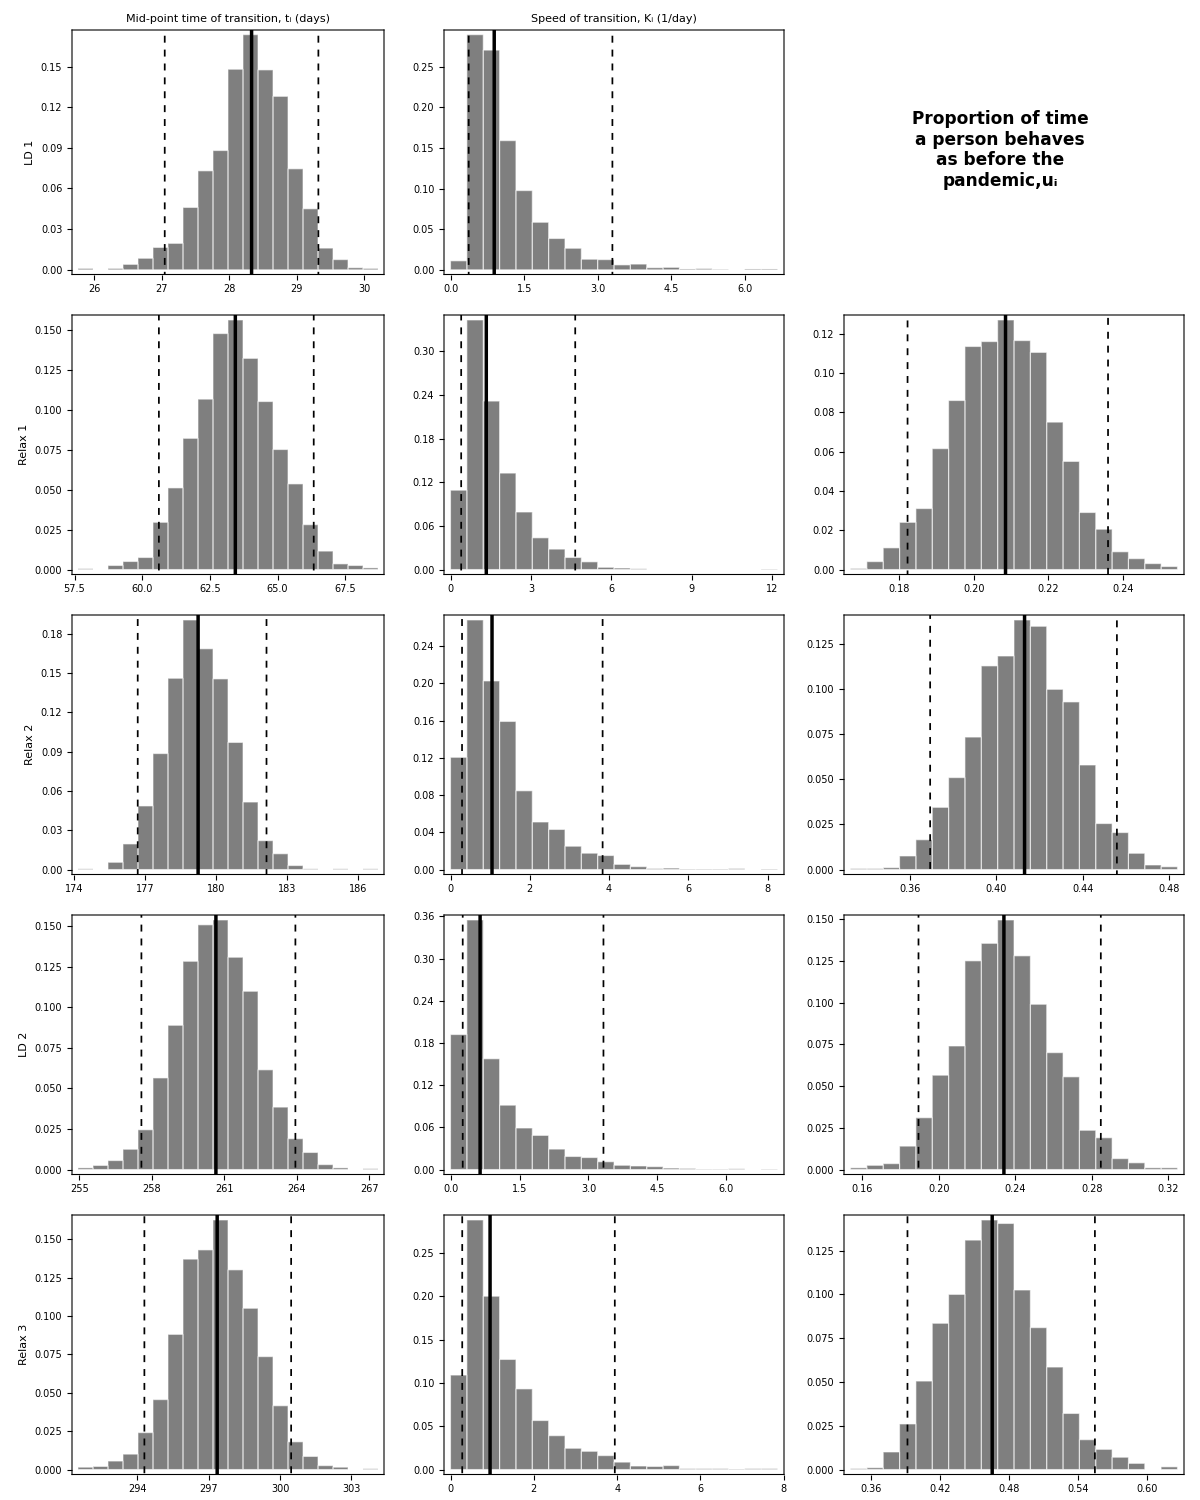

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figT = Table[plotWithLetter[plotHistogram[parameterTVals[[i]], If[i == 1, Style["Mid-point time of transition, \nt_i (days)", Bold], ""],
"", Style[diagramLabelsShort[[i]], Bold], Black, False], parameterTXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterTVals]}];
figK = Table[plotWithLetter[plotHistogram[parameterKVals[[i]], If[i == 1, Style["Speed of transition, \nK_i (1/day)", Bold], ""],"",  "", Black, False], parameterKXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterKVals]}];
figU = Table[plotWithLetter[plotHistogram[parameterUVals[[i]], "", "",  "", Black, False], parameterUXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterUVals]}];
figU = Prepend[figU, Graphics[Text[Style["Proportion of time\na person behaves\nas before the\npandemic,u_i\n\n\n\n\n", 17, Bold]]]];
figContParams = Grid[Transpose[{figT, figK, figU}]];

If[ifShowFigs, figContParams]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_PARAMETERS",  exportFormat[[i]]],figContParams], {i, 1, Length[exportFormat]}]];
```

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

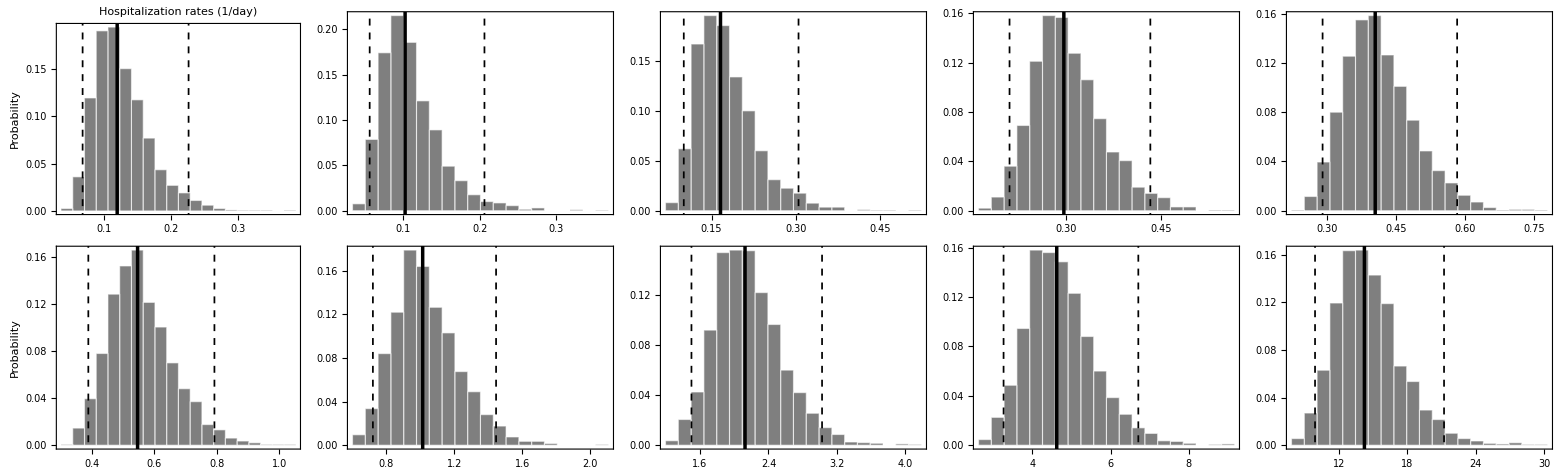

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figHospRates = Table[plotWithLetter[plotHistogram[parameterHospRateVals[[i]], If[i == 1, Style["Hospitalization rates (1/day)", Bold], ""],"",  If[i == 1 || i == 6, Style["Probability"],""], Black, False], ageLabelShort[[i]], Scaled[{0.8, 0.9}], sizeFontBig, colorDarkRainbow4AgeGroups[[i]]],{i, 1, Length[parameterHospRateVals]}];
figHospRates = Grid[ArrayReshape[figHospRates, {2,5}]];

If[ifShowFigs, figHospRates]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSP_RATES_PARAMETERS",  exportFormat[[i]]],figHospRates], {i, 1, Length[exportFormat]}]];
```

### HOSPITALIZATION DATA

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

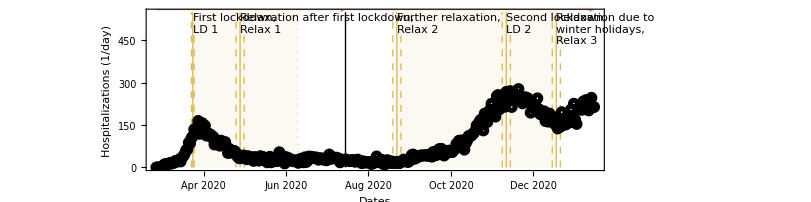

```mathematica
(* Importing data *)hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};

tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}][[All,{1,2}]];
ticksss={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
tickMonths = {#,DateString[DateObject[#],{"MonthNameShort"," ",""}]}&/@tickValues;

transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
transitionDatesLabelsLong={"First lockdown","Relaxation after first lockdown","Further relaxation","Second lockdown","Relaxation due to winter holidays"};
transitionDatesLabelsShort={"LD 1","Relax 1","Relax 2","LD 2","Relax 3"};

Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figDiag = plotDiagram[hospitalizationData, ticksss];
If[ifShowFigs, figDiag]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/DIAGRAM",  exportFormat[[i]]],figDiag], {i, 1, Length[exportFormat]}]];
```

## Scenarios

### SCHOOL REDUCTION FACTOR

```mathematica
(* Calculation of the zeta_school parameter for Scenario 2 *)
schoolReductionEquation := 
Table[If[!(k==9 || k==10 ||l==9||l==10||(l==3 && k==1)||(l==1 && k==3)),Solve[(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-reductionFactor Subscript[s,{k,l}]==(Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]),reductionFactor]⟦1⟧⟦1,2⟧],{k,1,numAgeGroups},{l,1,numAgeGroups}];
schoolReductionFactor[sample_]:=zetaSchools->Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]];

(* Table for all parameters *)
parametersComplete[sample_]:=
Join[parameters[sample],{schoolReductionFactor[sample]}];


SRFFilePath = FileNameJoin[{"../results/solutions/"},StringJoin["SCHOOL_REDUCTION_FACTOR.wxf"]];
schRedFacObtained= Module[{SRF},If[FileExistsQ[SRFFilePath],
SRF = Import[SRFFilePath,"WXF"],
SRF = Table[Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]], {sample, 1, numAllSamples}];
Export[SRFFilePath,SRF,"WXF","CompressionLevel"->5];
SRF]];
```

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

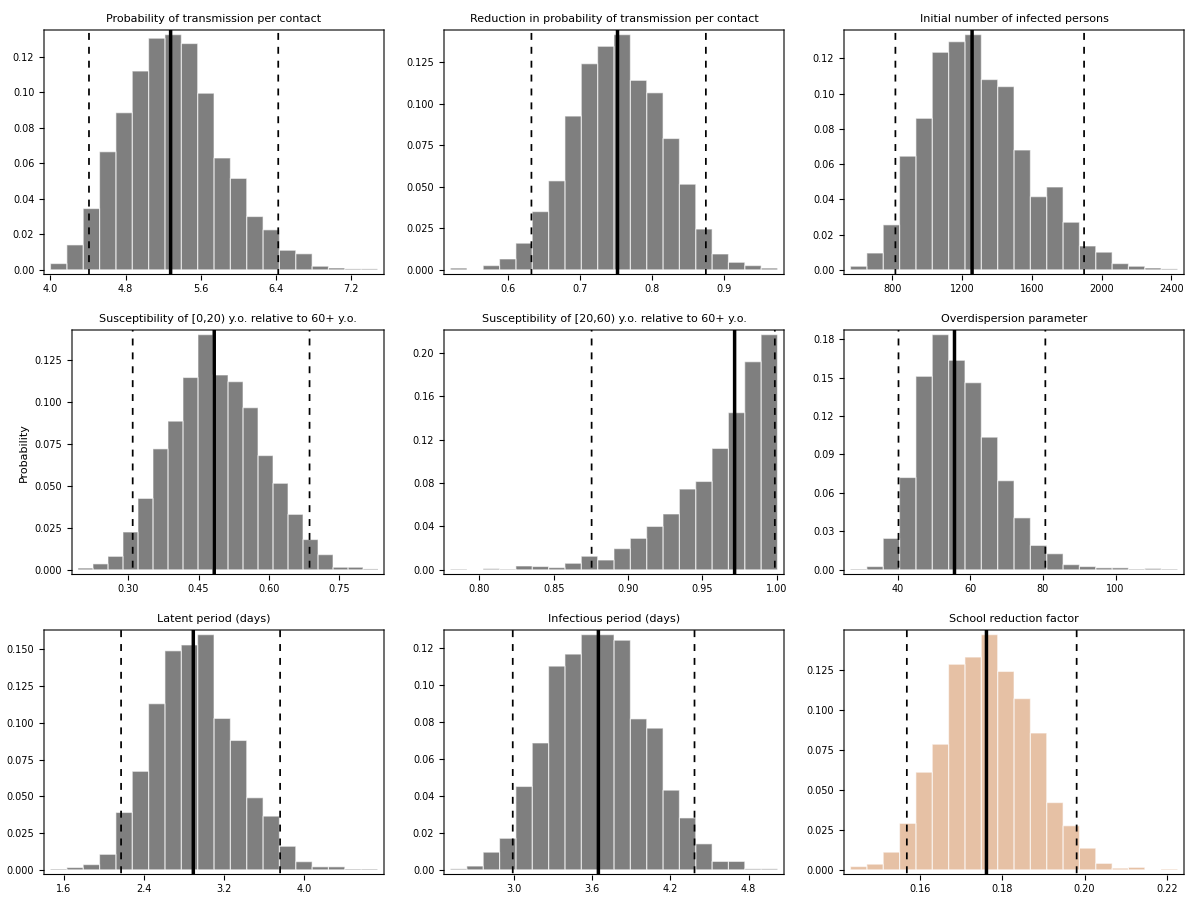

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figConstsTables = Table[plotWithLetter[plotHistogram[parameterConstVals[[i]], Style[parameterConstXLabel[[i]], Bold],
"", If[i == 4, Style["Probability", sizeFontBig], ""], Black, False], parameterConstXLabelShort[[i]], Which[i ==3, Scaled[{0.8, 0.9}], i == 5, Scaled[{0.2, 0.9}],True, "right"], sizeFontBig],{i, 1, Length[parameterConstVals]}];
figSRF = plotWithLetter[plotHistogram[schRedFacObtained, Style["School reduction factor", Bold],
"", "", colorOrange, False],"ζ_s", "right", sizeFontBig];
figConstsParams = Grid[ArrayReshape[{figConstsTables, figSRF}, {3,3}]];

If[ifShowFigs, figConstsParams]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONSTANTS_PARAMETERS",  exportFormat[[i]]],figConstsTables], {i, 1, Length[exportFormat]}]];
```

### EXPRESSIONS FOR CONTACT MATRICES

```mathematica
contactMatrixBaseline[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* SCENARIO 1 *)
(* Not closing schools during the first lockdown and closing them for school holidays on tstartschoolvacation (10 June)*)
(* ζ or Zeta schools can be introduced to reduce school contacts somewhat for the scenario with not closing schools after the first lockdown in 2020; the logic behind this is that there may be other measures implemented in schools such as masks, physical distancing, etc. *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1ZetaSchool[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ ζ 0.5*Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1RelaxedNS[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* Scenario 2 *)
(* Not opening schools after the summer holidays in 2020 *)
(* Zeta schools must be used to make sure that contacts are non-negative for the scenario with not opening schools after the summer holidays in 2020 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2ZetaZetaS[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2RelativeSchool[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) ((Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])* Subscript[s,{k,l}]/schoolContactsMultiplier) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) ((Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])- (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier)  (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) ((Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])-(Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier) ;
```

## Equations and variables

### MODEL EQUATIONS

```mathematica
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];

NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];

(*Table[Table[Subscript[λ,k][Intervention_/;Intervention==scenarios[[i]]][t]= ϵ Sum[scenarioContacts[[i]][t] (Subscript[II,l][t])/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups}], {i, 1, Length[scenarios]}];
*)
contactMatrixWhich[intervention_,t_]:=Which[intervention=="Baseline",contactMatrixBaseline[t],intervention=="Scenario1",contactMatrixScenario1[t],intervention=="Scenario2",contactMatrixScenario2[t],
intervention=="Scenario1_ZetaSchool",contactMatrixScenario1ZetaSchool[t],
intervention=="Scenario1_RelaxedNS",contactMatrixScenario1RelaxedNS[t],
intervention=="Scenario2_ZetaZetaS",contactMatrixScenario2ZetaZetaS[t],
intervention=="Scenario2_RelativeSchool",contactMatrixScenario2RelativeSchool[t],
True,$Failed ];

Table[Subscript[λ,k][intervention][t]=ε Sum[contactMatrixWhich[intervention,t] Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups},{intervention,scenarios} (*Iterate over interventions*)];

eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,numVariables},{k,listAgeGroups}];

eqsList[Intervention_]:=Flatten[Flatten[eqs[Intervention]]];
```

### VARIABLES

```mathematica
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totVars={totS,totEE,totII,totR,totH};
totVarsYLabel={"S(t)","E(t)","I(t)","R(t)","H(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)"};

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
```

### SOLVING THE MODEL

```mathematica
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];


solution[Intervention_,pars_]:=NDSolve[Join[eqsList[Intervention],ICsList]/.pars,varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
```

### HOSPITALIZATIONS, INCIDENCES, AND SUSCEPTIBLES

```mathematica
parametersCompleteSampled = Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];


solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions"];

trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,Subscript[t, step]}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions"]];


hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];


NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions"]];
hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPITALIZATION_SIMULATED"];


summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];

hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];
incidencesScenariosGrouped = summingGroups4Scenarios[incidencesScenarios, groupIndex];
incidencesScenariosTotal = summingGroups4Scenarios[incidencesScenarios, {Range[1, 10]}];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];



hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

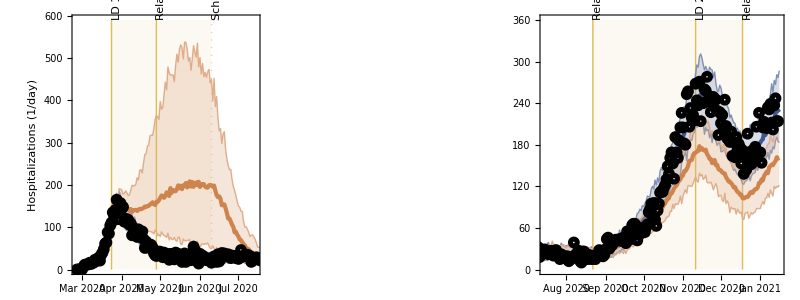

```mathematica
scatterPlotHospData = DateListPlot[Total[hospitalizationData,{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

figHosp = plotScenarioTrajectories[{hospitalizationSimulatedScenariosTotal[[1,1, All, All]],
hospitalizationSimulatedScenariosTotal[[2,1, All, All]],
hospitalizationSimulatedScenariosTotal[[3,1, All, All]]},"", "Hospitalizations (1/day)","",{ticksss,ticksss},{{0,590},{0,360}},scatterPlotHospData];
If[ifShowFigs, figHosp]
```

```mathematica
Dimensions[hospitalizationSimulatedScenariosGrouped]
```

{3,2,100,327}

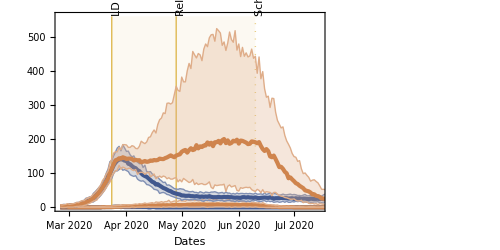

```mathematica
figHospTotal = plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],colorBlue,"","Dates","",1,ticksss,{0, 560}],plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],colorOrange],
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[1,2, All, All]],colorBlue,"","Dates","",1,ticksss,{0, 560}],plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[2,2, All, All]],colorOrange]},"A","left"]
```

```mathematica
seroprevalenceFunc[var_, varindices_, demogindices_] :=
Table[100-100var[[All,varindices[[i]],All,All]]/Total[demographyData10[[demogindices[[i]]]]], {i, 1, Length[varindices]}];

seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];

listGrouped = {Range[1,3], Range[4,10]};
seroprevalenceScenariosGrouped = ConstantArray[0, {3,2,100,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[listGrouped[[k]]]]];, {k ,1,2}];

seroprevalenceScenarios = ConstantArray[0, {3,10,100,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

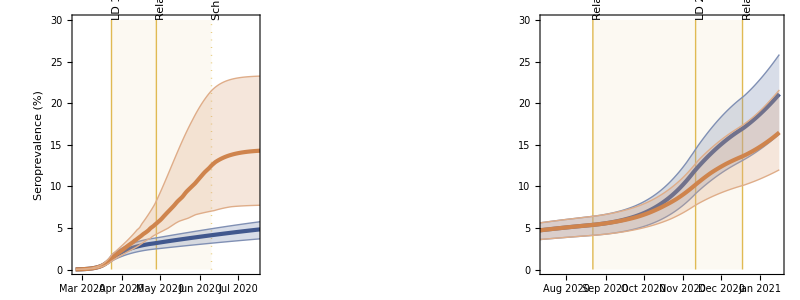

```mathematica
figSero = plotScenarioTrajectories[{seroprevalenceScenariosGrouped[[1,2, All, All]],
seroprevalenceScenariosGrouped[[2,2, All, All]],
seroprevalenceScenariosGrouped[[3,2, All, All]]},"","Seroprevalence (%)","",{ticksss,ticksss},{{0,30},{0,30}}];
If[ifShowFigs, figSero]
```

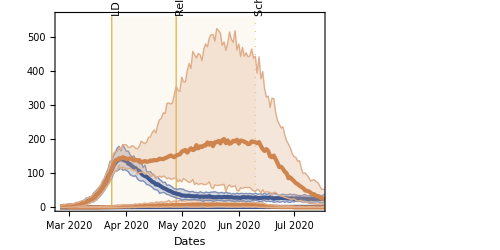

```mathematica
figSeroAges = plotWithLetter[{plotLineWithCrI[seroprevalenceScenarios[[1,1, All, All]],colorBlue,"","Dates","",1,ticksss,{0, 560}],plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],colorOrange],
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[1,2, All, All]],colorBlue,"","Dates","",1,ticksss,{0, 560}],plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[2,2, All, All]],colorOrange]},"A","left"]
```

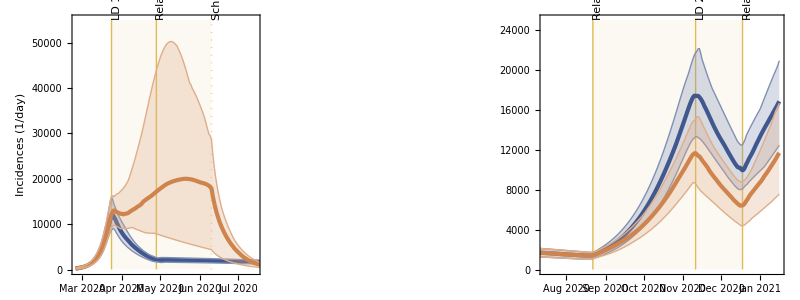

```mathematica
figIncid = plotScenarioTrajectories[{incidencesScenariosTotal[[1,1, All, All]],
incidencesScenariosTotal[[2,1, All, All]],
incidencesScenariosTotal[[3,1, All, All]]},"","Incidences (1/day)","",{ticksss,ticksss},{{0,55000},{0,25000}}];
If[ifShowFigs, figIncid]
```

## Analysis

### AVERAGE CONTACT RATE

```mathematica
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrixWhich[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];

importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,tStart,tEnd,Subscript[t, step]}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions"]];
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
demographyData1010 =Transpose[Table[demographyData10, {i, 1, numAgeGroups}]];
(*averageContactsTotalScenarios = Total[contactMatricesScenarios[[All, All, All, All, All]] * demographyData1010, {2}]*)
```

```mathematica
Dimensions[averageContactsTotalScenarios[#] & 1]
```

{1}

```mathematica
averageContactMatrixTotalScenarios = contactMatricesScenarios;
Do[averageContactMatrixTotalScenarios[[i,j,k,All,All]]=contactMatricesScenarios[[i,j,k,All,All]]*demographyData1010,{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];
averageContactsTotalScenarios = Total[averageContactMatrixTotalScenarios, {5}] / Total[demographyData10];
averageContactsTotalScenariosFunc[index_]:=averageContactsTotalScenarios[[index,All,All,All]];

importExportScenarioResults["CONTACTS_AVERAGE", averageContactsTotalScenariosFunc, "solutions"];
```

```mathematica
averageContactsTotal= Total[averageContactsTotalScenarios[[All, All, All, Range[1,10]]], {4}];
averageContactsChildren= Total[averageContactsTotalScenarios[[All, All, All, Range[1,3]]], {4}];
averageContactsAdults =Total[averageContactsTotalScenarios[[All, All, All, Range[4,10]]], {4}];
```

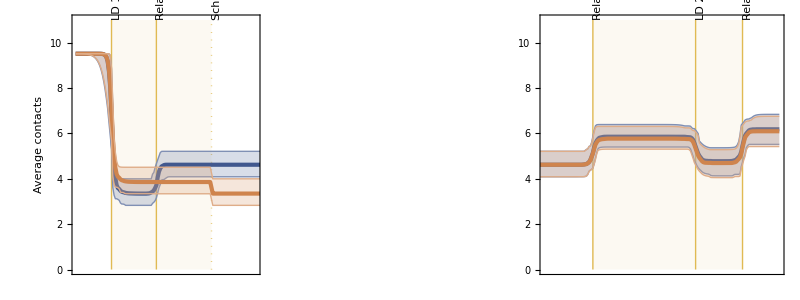

```mathematica
plotScenarioTrajectories[{averageContactsAdults[[1,All,All]],
averageContactsAdults[[2,All,All]],
averageContactsAdults[[3,All,All]]},"", "Average contacts","",{None, None},{{0,11},{0, 11}}, Graphics[], {"A", "B"}, "right"]
```

```mathematica
(* Creating the 2x2 contact matrices*)
transformList10to2[list10_]:=Total/@Join[{list10[[1;;3]]},{list10[[4;;10]]}];
demographyData2 = transformList10to2[demographyData10];
transformMatrix10to2[mat10_] :=transformList10to2[Transpose[transformList10to2[Transpose[mat10]]] demographyData10]/demographyData2;
```

```mathematica
twoContactMatrixScenarios = ConstantArray[0, {numScenarios, numSamples, numTimes, 2,2}];
Do[twoContactMatrixScenarios[[i,j,k,All,All]]=transformMatrix10to2[contactMatricesScenarios[[i,j,k,All,All]]],{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];
```

```mathematica
middleOfPeriodsScen1Dates = {"March 1, 2020", "April 1, 2020", "June 1, 2020", "July 1, 2020"};
middleOfPeriodsScen2Dates = {"August 1, 2020", "October 1, 2020", "December 1, 2020", "January 1, 2020"};
dateDifference[dateString_String]:=DateDifference[DateObject[{2020, 2,25}],DateObject[dateString],"Day"][[1]];
scen1Differences=dateDifference/@middleOfPeriodsScen1Dates;
scen2Differences=dateDifference/@middleOfPeriodsScen2Dates;
```

sizeFontBig::shdw: Symbol sizeFontBig appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorBlue::shdw: Symbol colorBlue appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorOrange::shdw: Symbol colorOrange appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

colorDarkRainbow4AgeGroups::shdw: Symbol colorDarkRainbow4AgeGroups appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

ageLabelShort::shdw: Symbol ageLabelShort appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotWithLetter::shdw: Symbol plotWithLetter appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

plotLineWithCrI::shdw: Symbol plotLineWithCrI appears in multiple contexts {plottingFunctions`,Global`}; definitions in context plottingFunctions` may shadow or be shadowed by other definitions.

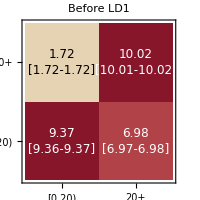
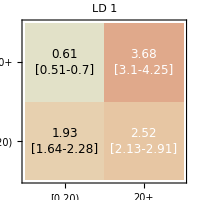
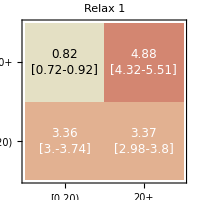
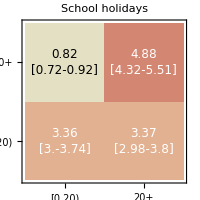
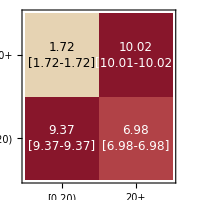
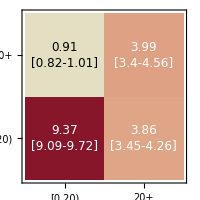
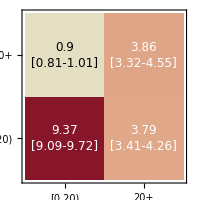
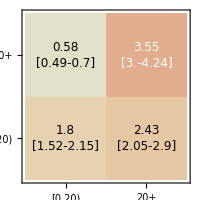
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

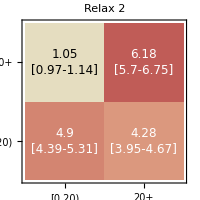
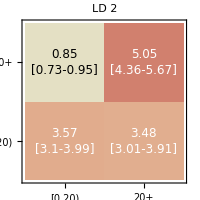
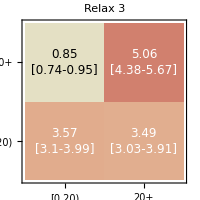
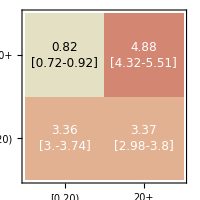
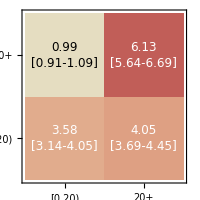
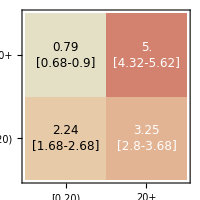
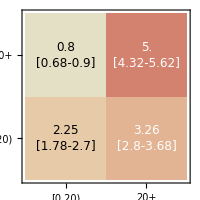
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

```mathematica
Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
twoConMatMedian = Median[Transpose[twoContactMatrixScenarios]];
twoConMatLower= Quantile[Transpose[twoContactMatrixScenarios], 0.025];
twoConMatUpper = Quantile[Transpose[twoContactMatrixScenarios], 0.975];
scen1CMTitles = Flatten[{"Before LD1", diagramLabelsShort[[1;;2]], "School holidays"}];
scen2CMTitles = diagramLabelsShort[[2;;5]];

figTwoCMScen1= Table[Table[plotMatrix2[twoConMatMedian[[j,scen1Differences[[i]]]],
twoConMatLower[[j,scen1Differences[[i]]]],
twoConMatUpper[[j,scen1Differences[[i]]]],
If[j === 1,scen1CMTitles[[i]], ""],False], {i, 1, Length[scen1Differences]}], {j, {1, 2}}];
figTwoCMScen2= Table[Table[plotMatrix2[twoConMatMedian[[j,scen2Differences[[i]]]],
twoConMatLower[[j,scen2Differences[[i]]]],
twoConMatUpper[[j,scen2Differences[[i]]]],
If[j === 1,scen2CMTitles[[i]], ""],False], {i, 1, Length[scen2Differences]}], {j, {1, 3}}];
fig2CMScenario1 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen1[[1]]}], Flatten[{Style[Rotate["Scenario 1", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen1[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}]
fig2CMScenario2 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen2[[1]]}], Flatten[{Style[Rotate["Scenario 2", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen2[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}]
```

### TIME-VARYING REPRODUCTION NUMBER

```mathematica
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];
```

```mathematica
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;

NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,tStart,tEnd,Subscript[t, step]}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop, "analysis"];

eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop, "analysis"];
```

### TIME-VARYING CUMULATIVE ELASTICITIES

```mathematica
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];

elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];

cumuElasMatrix[elas_] :=
Total[elas,{1}];

sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];

sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop, "analysis"];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop, "analysis"];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop, "analysis"];


cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

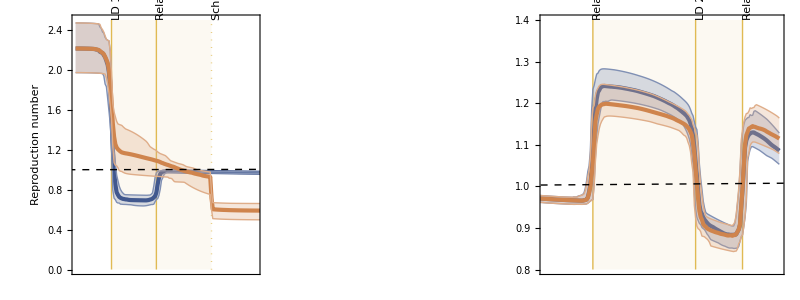
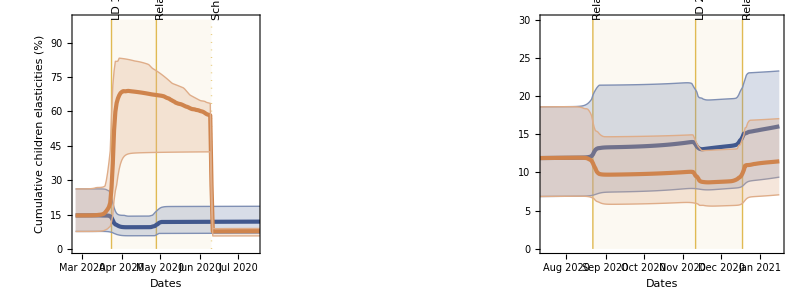

```mathematica
tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}][[All,{1,2}]];
ticksss={#,Rotate[DateString[#,{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

Rt1 = Graphics[{Dashed,Black,InfiniteLine[{AbsoluteTime["February 26, 2020"],1},{AbsoluteTime["January 15, 2020"],1}]}];

figRt = plotScenarioTrajectories[{RtScenarios[[1,All,All,1]],
RtScenarios[[2,All,All,1]],
RtScenarios[[3,All,All,1]]},"", "Reproduction number","",{None, None},{{0,2.5},{0.8,1.4}}, Rt1, {"A", "B"}, "right"];
figCumuElas = plotScenarioTrajectories[{100cumuElasGroupedScenarios[[1,All,All,1]],
100cumuElasGroupedScenarios[[2,All,All,1]],
100cumuElasGroupedScenarios[[3,All,All,1]]},"Dates","Cumulative children elasticities (%)","",{ticksss,ticksss},{{0,100},{0, 30}},  Graphics[],{"C", "D"}, "right"];
Grid[{{figRt}, {figCumuElas}}]
```

### PARAMETER ELASTICITIES

```mathematica
susceptibilitySymbol = Table[Subscript[β,k], {k, 1, numAgeGroups}];
hospitalizationRateSymbol = Table[Subscript[ν,k], {k, 1, numAgeGroups}];
contactSymbol = Table[Subscript[c, {k, l}], {k, 1, numAgeGroups}, {l, 1, numAgeGroups}];
(*parameterSymbols = {susceptibilitySymbol, hospitalizationRateSymbol, contactSymbol};*)
parameterSymbols = {susceptibilitySymbol};
parameterSymbols = Flatten[parameterSymbols];

NGMContactInvariant = Table[NGM[[1]][[k]] /. {Table[contactMatrixBaseline[t] -> Subscript[c, {k, l}],{l, 1, numAgeGroups}]}[[1]], {k, 1, numAgeGroups}];
NGMContactInvariant = Simplify[NGMContactInvariant];

NGMContactInvariant // MatrixForm
```

((ε c_{1,1} β_1 S_1[t])/(NN_1 (γ+ν_1)) | (ε c_{1,2} β_1 S_1[t])/(NN_2 (γ+ν_2)) | (ε c_{1,3} β_1 S_1[t])/(NN_3 (γ+ν_3)) | (ε c_{1,4} β_1 S_1[t])/(NN_4 (γ+ν_4)) | (ε c_{1,5} β_1 S_1[t])/(NN_5 (γ+ν_5)) | (ε c_{1,6} β_1 S_1[t])/(NN_6 (γ+ν_6)) | (ε c_{1,7} β_1 S_1[t])/(NN_7 (γ+ν_7)) | (ε c_{1,8} β_1 S_1[t])/(NN_8 (γ+ν_8)) | (ε c_{1,9} β_1 S_1[t])/(NN_9 (γ+ν_9)) | (ε c_{1,10} β_1 S_1[t])/(NN_10 (γ+ν_10))
(ε c_{2,1} β_2 S_2[t])/(NN_1 (γ+ν_1)) | (ε c_{2,2} β_2 S_2[t])/(NN_2 (γ+ν_2)) | (ε c_{2,3} β_2 S_2[t])/(NN_3 (γ+ν_3)) | (ε c_{2,4} β_2 S_2[t])/(NN_4 (γ+ν_4)) | (ε c_{2,5} β_2 S_2[t])/(NN_5 (γ+ν_5)) | (ε c_{2,6} β_2 S_2[t])/(NN_6 (γ+ν_6)) | (ε c_{2,7} β_2 S_2[t])/(NN_7 (γ+ν_7)) | (ε c_{2,8} β_2 S_2[t])/(NN_8 (γ+ν_8)) | (ε c_{2,9} β_2 S_2[t])/(NN_9 (γ+ν_9)) | (ε c_{2,10} β_2 S_2[t])/(NN_10 (γ+ν_10))
(ε c_{3,1} β_3 S_3[t])/(NN_1 (γ+ν_1)) | (ε c_{3,2} β_3 S_3[t])/(NN_2 (γ+ν_2)) | (ε c_{3,3} β_3 S_3[t])/(NN_3 (γ+ν_3)) | (ε c_{3,4} β_3 S_3[t])/(NN_4 (γ+ν_4)) | (ε c_{3,5} β_3 S_3[t])/(NN_5 (γ+ν_5)) | (ε c_{3,6} β_3 S_3[t])/(NN_6 (γ+ν_6)) | (ε c_{3,7} β_3 S_3[t])/(NN_7 (γ+ν_7)) | (ε c_{3,8} β_3 S_3[t])/(NN_8 (γ+ν_8)) | (ε c_{3,9} β_3 S_3[t])/(NN_9 (γ+ν_9)) | (ε c_{3,10} β_3 S_3[t])/(NN_10 (γ+ν_10))
(ε c_{4,1} β_4 S_4[t])/(NN_1 (γ+ν_1)) | (ε c_{4,2} β_4 S_4[t])/(NN_2 (γ+ν_2)) | (ε c_{4,3} β_4 S_4[t])/(NN_3 (γ+ν_3)) | (ε c_{4,4} β_4 S_4[t])/(NN_4 (γ+ν_4)) | (ε c_{4,5} β_4 S_4[t])/(NN_5 (γ+ν_5)) | (ε c_{4,6} β_4 S_4[t])/(NN_6 (γ+ν_6)) | (ε c_{4,7} β_4 S_4[t])/(NN_7 (γ+ν_7)) | (ε c_{4,8} β_4 S_4[t])/(NN_8 (γ+ν_8)) | (ε c_{4,9} β_4 S_4[t])/(NN_9 (γ+ν_9)) | (ε c_{4,10} β_4 S_4[t])/(NN_10 (γ+ν_10))
(ε c_{5,1} β_5 S_5[t])/(NN_1 (γ+ν_1)) | (ε c_{5,2} β_5 S_5[t])/(NN_2 (γ+ν_2)) | (ε c_{5,3} β_5 S_5[t])/(NN_3 (γ+ν_3)) | (ε c_{5,4} β_5 S_5[t])/(NN_4 (γ+ν_4)) | (ε c_{5,5} β_5 S_5[t])/(NN_5 (γ+ν_5)) | (ε c_{5,6} β_5 S_5[t])/(NN_6 (γ+ν_6)) | (ε c_{5,7} β_5 S_5[t])/(NN_7 (γ+ν_7)) | (ε c_{5,8} β_5 S_5[t])/(NN_8 (γ+ν_8)) | (ε c_{5,9} β_5 S_5[t])/(NN_9 (γ+ν_9)) | (ε c_{5,10} β_5 S_5[t])/(NN_10 (γ+ν_10))
(ε c_{6,1} β_6 S_6[t])/(NN_1 (γ+ν_1)) | (ε c_{6,2} β_6 S_6[t])/(NN_2 (γ+ν_2)) | (ε c_{6,3} β_6 S_6[t])/(NN_3 (γ+ν_3)) | (ε c_{6,4} β_6 S_6[t])/(NN_4 (γ+ν_4)) | (ε c_{6,5} β_6 S_6[t])/(NN_5 (γ+ν_5)) | (ε c_{6,6} β_6 S_6[t])/(NN_6 (γ+ν_6)) | (ε c_{6,7} β_6 S_6[t])/(NN_7 (γ+ν_7)) | (ε c_{6,8} β_6 S_6[t])/(NN_8 (γ+ν_8)) | (ε c_{6,9} β_6 S_6[t])/(NN_9 (γ+ν_9)) | (ε c_{6,10} β_6 S_6[t])/(NN_10 (γ+ν_10))
(ε c_{7,1} β_7 S_7[t])/(NN_1 (γ+ν_1)) | (ε c_{7,2} β_7 S_7[t])/(NN_2 (γ+ν_2)) | (ε c_{7,3} β_7 S_7[t])/(NN_3 (γ+ν_3)) | (ε c_{7,4} β_7 S_7[t])/(NN_4 (γ+ν_4)) | (ε c_{7,5} β_7 S_7[t])/(NN_5 (γ+ν_5)) | (ε c_{7,6} β_7 S_7[t])/(NN_6 (γ+ν_6)) | (ε c_{7,7} β_7 S_7[t])/(NN_7 (γ+ν_7)) | (ε c_{7,8} β_7 S_7[t])/(NN_8 (γ+ν_8)) | (ε c_{7,9} β_7 S_7[t])/(NN_9 (γ+ν_9)) | (ε c_{7,10} β_7 S_7[t])/(NN_10 (γ+ν_10))
(ε c_{8,1} β_8 S_8[t])/(NN_1 (γ+ν_1)) | (ε c_{8,2} β_8 S_8[t])/(NN_2 (γ+ν_2)) | (ε c_{8,3} β_8 S_8[t])/(NN_3 (γ+ν_3)) | (ε c_{8,4} β_8 S_8[t])/(NN_4 (γ+ν_4)) | (ε c_{8,5} β_8 S_8[t])/(NN_5 (γ+ν_5)) | (ε c_{8,6} β_8 S_8[t])/(NN_6 (γ+ν_6)) | (ε c_{8,7} β_8 S_8[t])/(NN_7 (γ+ν_7)) | (ε c_{8,8} β_8 S_8[t])/(NN_8 (γ+ν_8)) | (ε c_{8,9} β_8 S_8[t])/(NN_9 (γ+ν_9)) | (ε c_{8,10} β_8 S_8[t])/(NN_10 (γ+ν_10))
(ε c_{9,1} β_9 S_9[t])/(NN_1 (γ+ν_1)) | (ε c_{9,2} β_9 S_9[t])/(NN_2 (γ+ν_2)) | (ε c_{9,3} β_9 S_9[t])/(NN_3 (γ+ν_3)) | (ε c_{9,4} β_9 S_9[t])/(NN_4 (γ+ν_4)) | (ε c_{9,5} β_9 S_9[t])/(NN_5 (γ+ν_5)) | (ε c_{9,6} β_9 S_9[t])/(NN_6 (γ+ν_6)) | (ε c_{9,7} β_9 S_9[t])/(NN_7 (γ+ν_7)) | (ε c_{9,8} β_9 S_9[t])/(NN_8 (γ+ν_8)) | (ε c_{9,9} β_9 S_9[t])/(NN_9 (γ+ν_9)) | (ε c_{9,10} β_9 S_9[t])/(NN_10 (γ+ν_10))
(ε c_{10,1} β_10 S_10[t])/(NN_1 (γ+ν_1)) | (ε c_{10,2} β_10 S_10[t])/(NN_2 (γ+ν_2)) | (ε c_{10,3} β_10 S_10[t])/(NN_3 (γ+ν_3)) | (ε c_{10,4} β_10 S_10[t])/(NN_4 (γ+ν_4)) | (ε c_{10,5} β_10 S_10[t])/(NN_5 (γ+ν_5)) | (ε c_{10,6} β_10 S_10[t])/(NN_6 (γ+ν_6)) | (ε c_{10,7} β_10 S_10[t])/(NN_7 (γ+ν_7)) | (ε c_{10,8} β_10 S_10[t])/(NN_8 (γ+ν_8)) | (ε c_{10,9} β_10 S_10[t])/(NN_9 (γ+ν_9)) | (ε c_{10,10} β_10 S_10[t])/(NN_10 (γ+ν_10)))

```mathematica
betaVals = {estimatesData[[listSamples, 14]], 
estimatesData[[listSamples, 14]],
estimatesData[[listSamples, 14]],
estimatesData[[listSamples, 15]],
estimatesData[[listSamples, 15]],
estimatesData[[listSamples, 15]],
estimatesData[[listSamples, 15]],
estimatesData[[listSamples, 16]],
estimatesData[[listSamples, 16]],
estimatesData[[listSamples, 16]]};
betaScenarios = Table[Table[betaVals[[i,j]],{j,1,Length[listSamples]}],{i,1,numAgeGroups},{k,1,numAgeGroups}];
betaScenarios = Table[Table[betaScenarios, {i, 1, numScenarios}], {t, 1, Length[times]}];
betaScenarios = Transpose[betaScenarios, {3, 1, 4, 5, 2}];
```

```mathematica
susceptibleFracScenarios = Table[susceptibleScenarios[[i,k,sample,t]]/demographyData10[[l]],{i,1,numScenarios},{sample,1,numSamples},{t,1,Length[times]},{k,1,numAgeGroups}, {l,1,numAgeGroups}];
susceptibleFracScenariosTotal = Table[Total[susceptibleScenarios[[i,All,All,All]]]/Total[demographyData10[[All]]],{i,1,numScenarios}];
```

```mathematica
figSusc = plotScenarioTrajectories[{100susceptibleFracScenariosTotal[[1, All, All]],
100susceptibleFracScenariosTotal[[2, All, All]],
100susceptibleFracScenariosTotal[[3, All, All]]},"Susceptible (%)","",{ticksss,ticksss},{{70,100},{70,100}}];
If[ifShowFigs, figSusc]
```

-Graphics-

```mathematica
parameterMultiplyVals = {betaScenarios, contactMatricesScenarios, susceptibleFracScenarios};
```

```mathematica
partialNGMpartialParam = Table[(1/parameterMultiplyVals[[i]]) * NGMScenarios,{i, 1, Length[parameterMultiplyVals]}];
sensTimesPartialNGMPartialParam =Table[partialNGMpartialParam[[i]] * sensScenarios,{i, 1, Length[parameterMultiplyVals]}];

RtScenariosDivider = Table[RtScenarios[[All, All, All, 1]], {k,1,numAgeGroups}, {l,1,numAgeGroups}];
RtScenariosDivider = Transpose[RtScenariosDivider, {4, 5, 1,2, 3}];
elasTimesPartialNGMPartialParam =Table[sensTimesPartialNGMPartialParam[[i,j]] * parameterMultiplyVals[[i,j]]/RtScenariosDivider[[j]] ,{i, 1, Length[parameterMultiplyVals]}, {j, 1, numScenarios}];
```

```mathematica
sensParamsSummed = Total[sensTimesPartialNGMPartialParam, {5, 6}];
elasParamsSummed = Total[elasTimesPartialNGMPartialParam, {5}];
```

```mathematica
susceptibleFracScenarios[[1,1,1]] // MatrixForm
```

(0.999891 | 0.939271 | 0.410044 | 0.396752 | 0.346504 | 0.275062 | 0.292341 | 0.335022 | 0.445252 | 0.64799
1.06439 | 0.999864 | 0.436496 | 0.422347 | 0.368857 | 0.292807 | 0.3112 | 0.356635 | 0.473975 | 0.689792
2.43817 | 2.29035 | 0.999864 | 0.967452 | 0.844925 | 0.67072 | 0.712854 | 0.816929 | 1.08572 | 1.58008
2.51985 | 2.36708 | 1.03336 | 0.999864 | 0.873232 | 0.693191 | 0.736736 | 0.844298 | 1.12209 | 1.63301
2.88527 | 2.71034 | 1.18321 | 1.14486 | 0.999864 | 0.793714 | 0.843574 | 0.966734 | 1.28481 | 1.86983
3.63465 | 3.41429 | 1.49053 | 1.44221 | 1.25956 | 0.999864 | 1.06267 | 1.21782 | 1.61851 | 2.35547
3.41982 | 3.21249 | 1.40243 | 1.35697 | 1.18511 | 0.940767 | 0.999864 | 1.14584 | 1.52285 | 2.21625
2.98414 | 2.80323 | 1.22376 | 1.18409 | 1.03413 | 0.820915 | 0.872483 | 0.999864 | 1.32884 | 1.93391
2.24537 | 2.10924 | 0.920801 | 0.890952 | 0.778114 | 0.617684 | 0.656485 | 0.752331 | 0.999864 | 1.45514
1.54286 | 1.44932 | 0.632708 | 0.612198 | 0.534664 | 0.424428 | 0.451089 | 0.516948 | 0.687035 | 0.999864)

```mathematica
susceptibleScenarios[[1, All, 1,1]]/Total[susceptibleScenarios[[1, All, 1,1]]]
```

{0.0421283,0.044846,0.102727,0.106169,0.121565,0.153138,0.144087,0.125731,0.094604,0.065005}

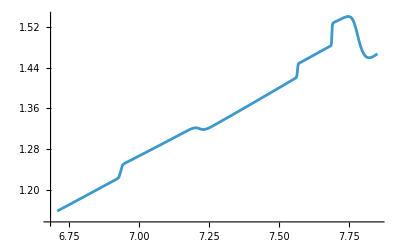

```mathematica
ListLinePlot[Transpose[{Total[susceptibleFracScenarios[[1,1,All, 10]], {2}],sensParamsSummed[[2,1,1,All]]}]]
```

```mathematica
Show[{plotLineWithCrI[elasParamsSummed[[2,1,All,All,1]],"","Dates","",colorBlue,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0,0.5}],
plotLineWithCrI[elasParamsSummed[[2,1,All,All,2]],"","Dates","",colorOrange,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0,0.5}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[3,1,All,All]],"","Dates","",colorBlue,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[3,2,All,All]],"","Dates","",colorOrange,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
colorDarkRainbow
```

{RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.253651, 0.344893, 0.558151],RGBColor[0.264425, 0.423024, 0.3849],RGBColor[0.29146900000000003, 0.47717000000000004, 0.271411],RGBColor[0.416394, 0.555345, 0.24182],RGBColor[0.624866, 0.673302, 0.264296],RGBColor[0.8130330000000001, 0.766292, 0.303458],RGBColor[0.8778749999999998, 0.7310449999999997, 0.326896],RGBColor[0.812807, 0.518694, 0.303459],RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.72987, 0.239399, 0.230961]}

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[1,1,All,All]],"","Dates","",colorBlue,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[2,1,All,All]],"","Dates","",colorYellow,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[3,1,All,All]],"","Dates","",colorGreen,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[1,2,All,All]],"","Dates","",colorBlue,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[2,2,All,All]],"","Dates","",colorYellow,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[3,2,All,All]],"","Dates","",colorGreen,Subscript[t, start,1], Subscript[t, end,1],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,1)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[1,1,All,All]],"","Dates","",colorBlue,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.75,1.75}],
plotLineWithCrI[sensParamsSummed[[2,1,All,All]],"","Dates","",colorYellow,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[3,1,All,All]],"","Dates","",colorGreen,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[1,3,All,All]],"","Dates","",colorBlue,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.75,1.75}],
plotLineWithCrI[sensParamsSummed[[2,3,All,All]],"","Dates","",colorYellow,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.5,3}],
plotLineWithCrI[sensParamsSummed[[3,3,All,All]],"","Dates","",colorGreen,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{plotLineWithCrI[sensParamsSummed[[3,1,All,All]],"","Dates","",colorBlue,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.75,1.75}],
plotLineWithCrI[sensParamsSummed[[3,3,All,All]],"","Dates","",colorOrange,Subscript[t, start,2], Subscript[t, end,2],ticksss,{0.5,3}]}]
```

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Lighter::arg: should be a valid color directive, an image, or a list of them.

General::stop: Further output of Lighter::arg will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {If[t_(start,2)==1,{tStart1,tEnd1},{tStart2,tEnd2}],{{{2020,3},Mar 2020},{{2020,4},Apr 2020},{{2020,5},May 2020},{{2020,6},Jun 2020},{{2020,7},Jul 2020},{{2020,8},Aug 2020},{{2020,9},Sep 2020},{{2020,10},Oct 2020},{{2020,11},Nov 2020},{{2020,12},Dec 2020},{{2021,1},Jan 2021}}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Dimensions[sensTimesPartialNGMPartialParam]
```

{3,3,100,327,10,10}

```mathematica
(*plotMatrix[Median[sensTimesPartialNGMPartialParam[[4,3,All,50]]], "ThermometerColors" ,"", "sensitivity"]*)
```

## Extra figures for two scenarios

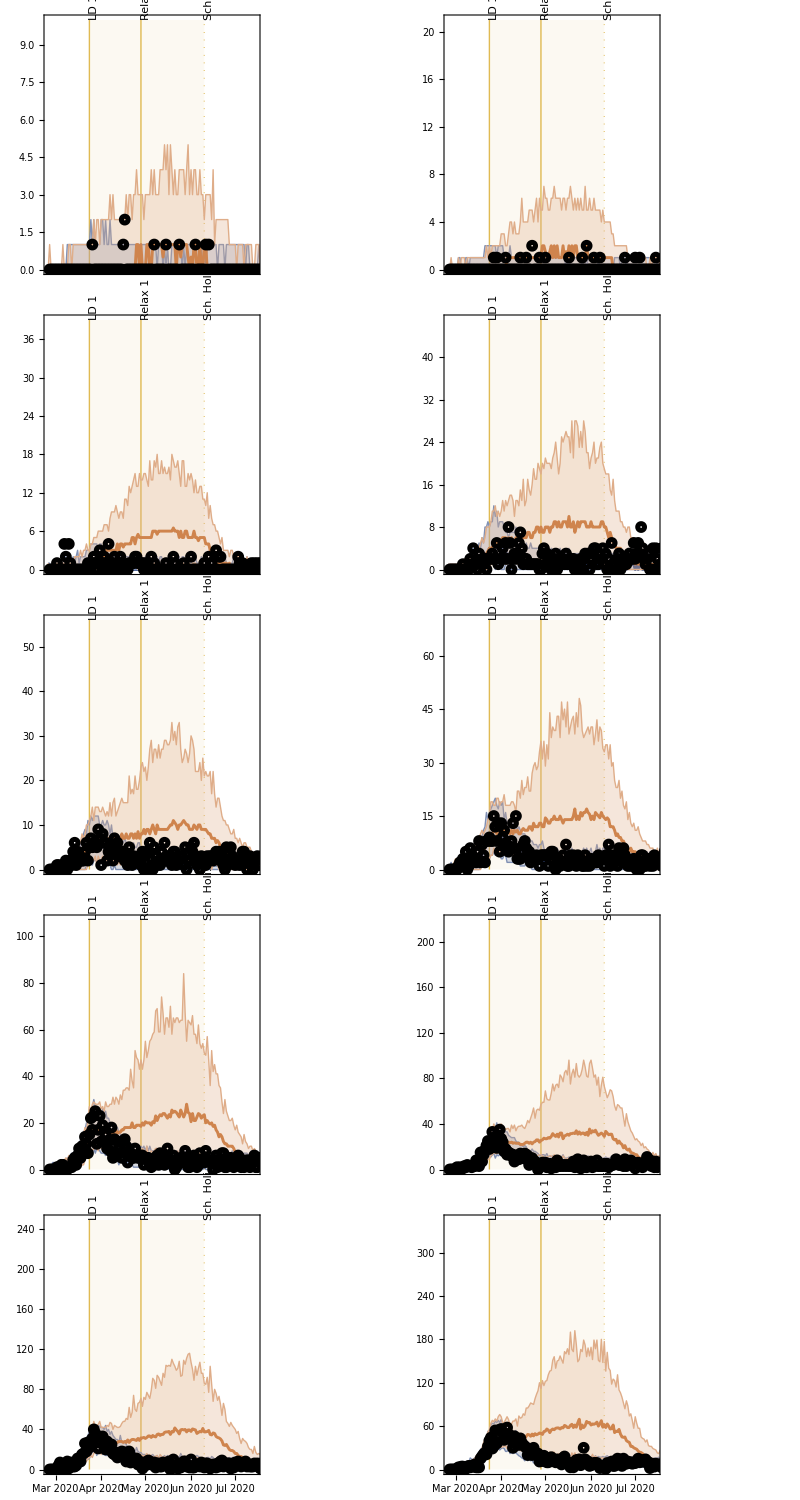
Hospitalizations (1/day) | -Graphics-
 | Dates

```mathematica
scatterPlotHospData10Groups[k_] := DateListPlot[hospitalizationData[[All,k]], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

figHosp10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[hospitalizationSimulatedScenarios[[2, k, All, All]]];
maxRange = maxVal+10^Floor[Log10[Abs[maxVal]]];
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[hospitalizationSimulatedScenarios[[2, k, All, All]],colorOrange],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figHosp10Scen1 = Grid[{{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figHosp10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSPITALIZATIONS_10_SCEN1",  exportFormat[[i]]],figHosp10Scen1], {i, 1, Length[exportFormat]}]];
```

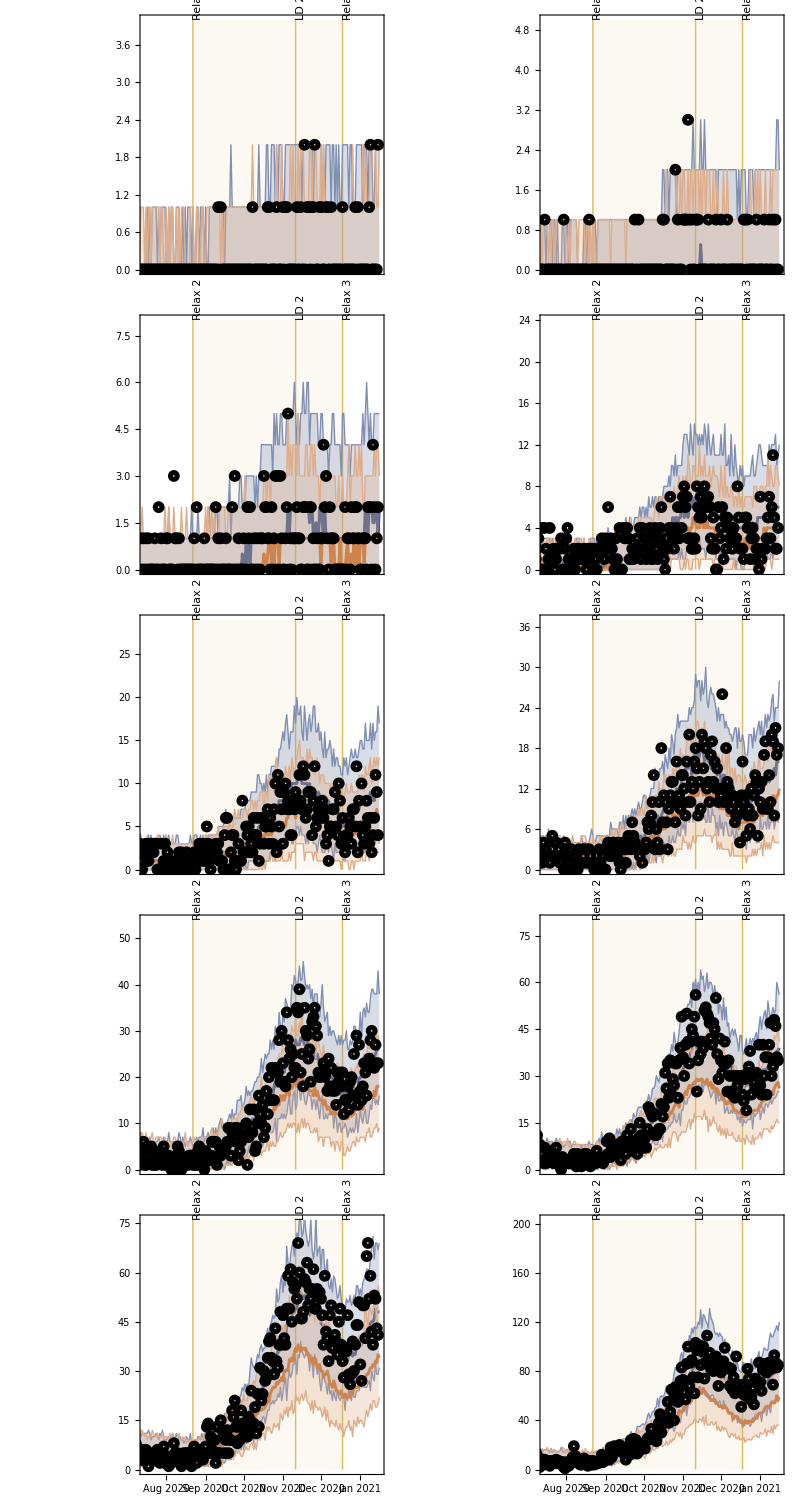
Hospitalizations (1/day) | -Graphics-
 | Dates

```mathematica
figHosp10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[hospitalizationSimulatedScenarios[[3, k, All, All]]];
maxRange = maxVal+10^Floor[Log10[Abs[maxVal]]];
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[hospitalizationSimulatedScenarios[[3, k, All, All]],colorOrange],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figHosp10Scen2 = Grid[{{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figHosp10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSPITALIZATIONS_10_SCEN2",  exportFormat[[i]]],figHosp10Scen2], {i, 1, Length[exportFormat]}]];
```

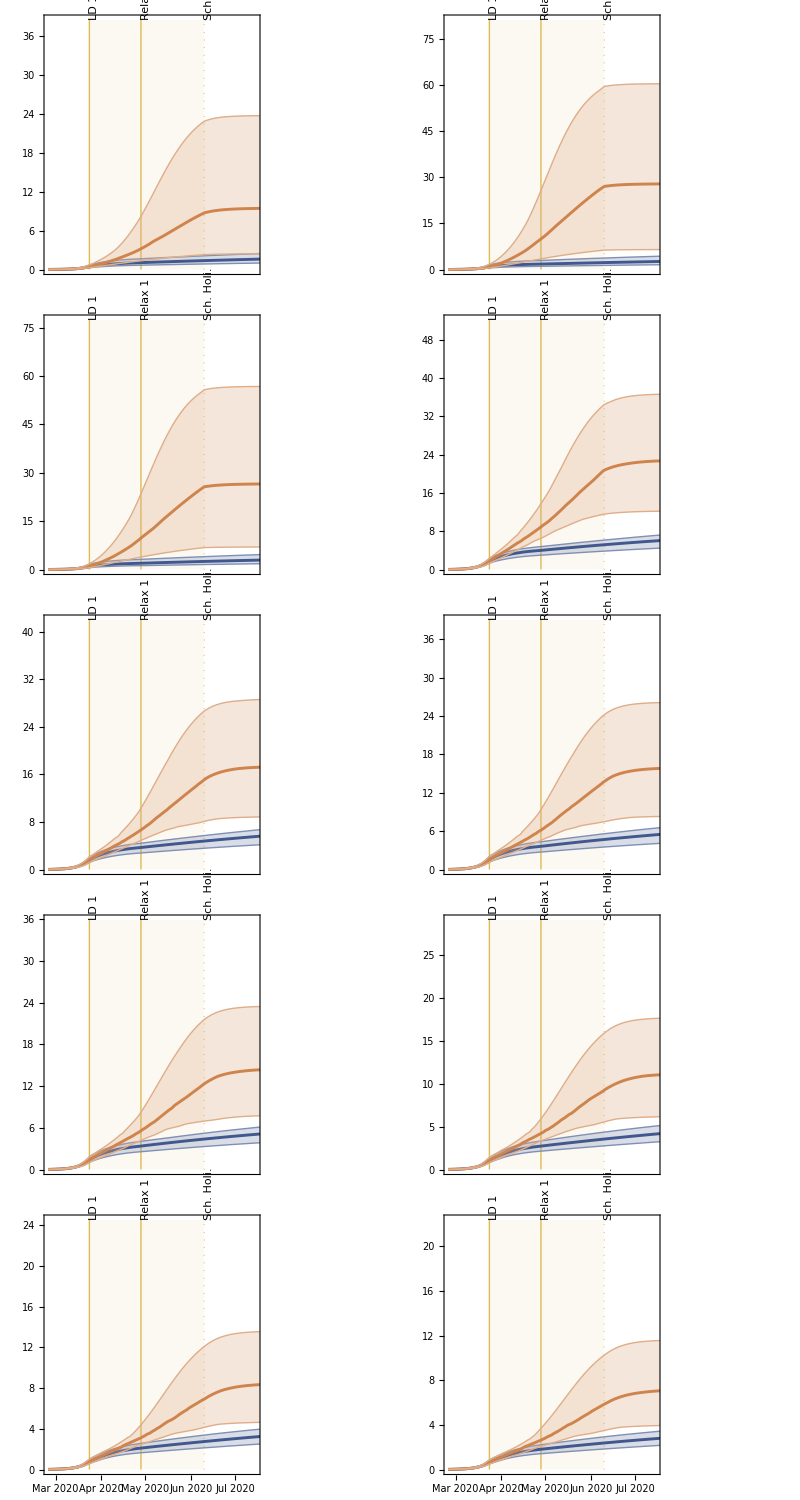
Seroprevalence (%) | -Graphics-
 | Dates

```mathematica
figSero10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[seroprevalenceScenarios[[2, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[seroprevalenceScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[seroprevalenceScenarios[[2, k, All, All]],colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figSero10Scen1 = Grid[{{Style[Rotate["Seroprevalence (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figSero10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSero10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SEROPREVALENCE_10_SCEN1",  exportFormat[[i]]],figSero10Scen1], {i, 1, Length[exportFormat]}]];
```

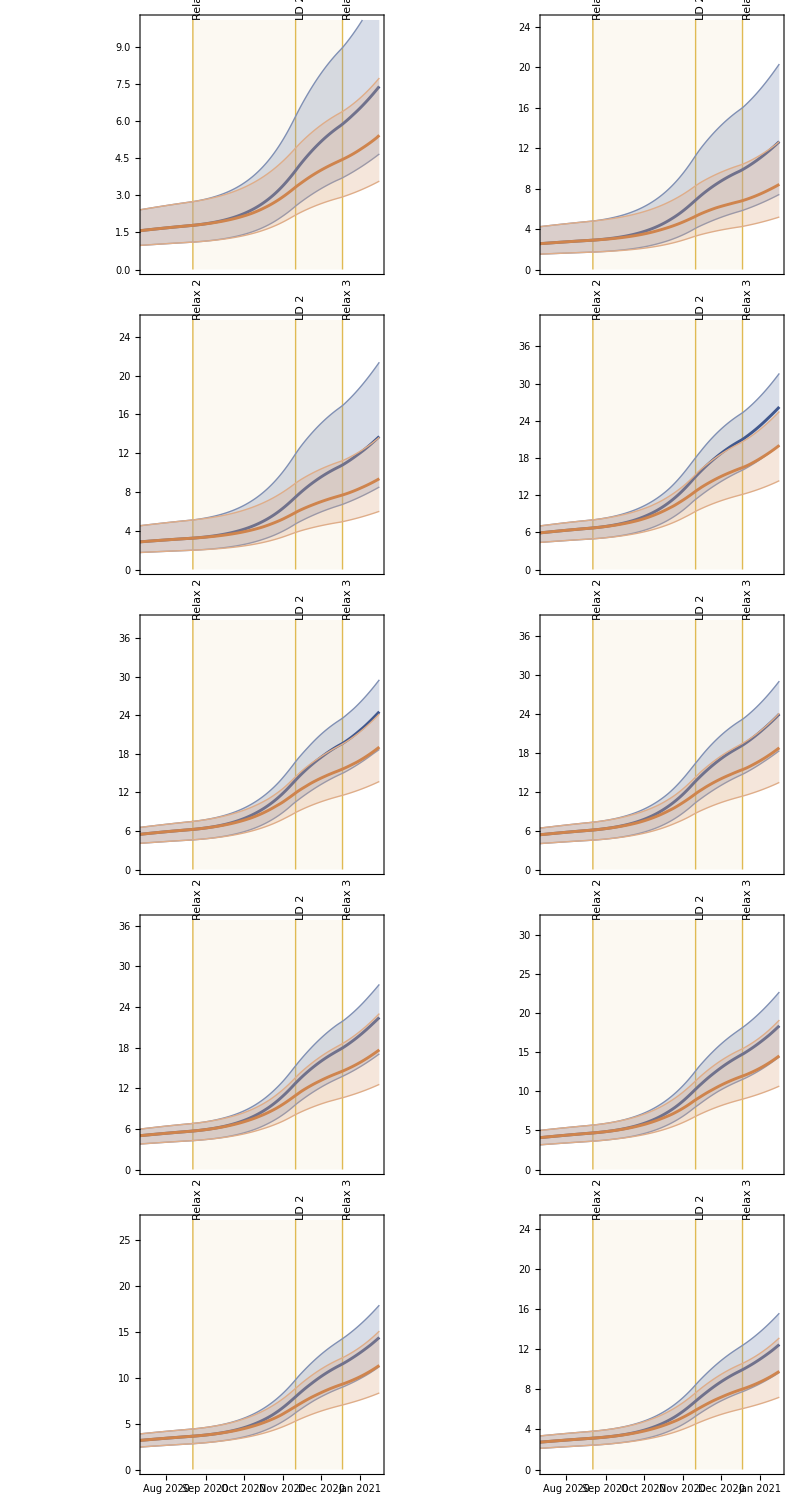
Seroprevalence (%) | -Graphics-
 | Dates

```mathematica
figSero10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[seroprevalenceScenarios[[3, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[seroprevalenceScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[seroprevalenceScenarios[[3, k, All, All]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figSero10Scen2 = Grid[{{Style[Rotate["Seroprevalence (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figSero10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSero10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SEROPREVALENCE_10_SCEN2",  exportFormat[[i]]],figSero10Scen2], {i, 1, Length[exportFormat]}]];
```

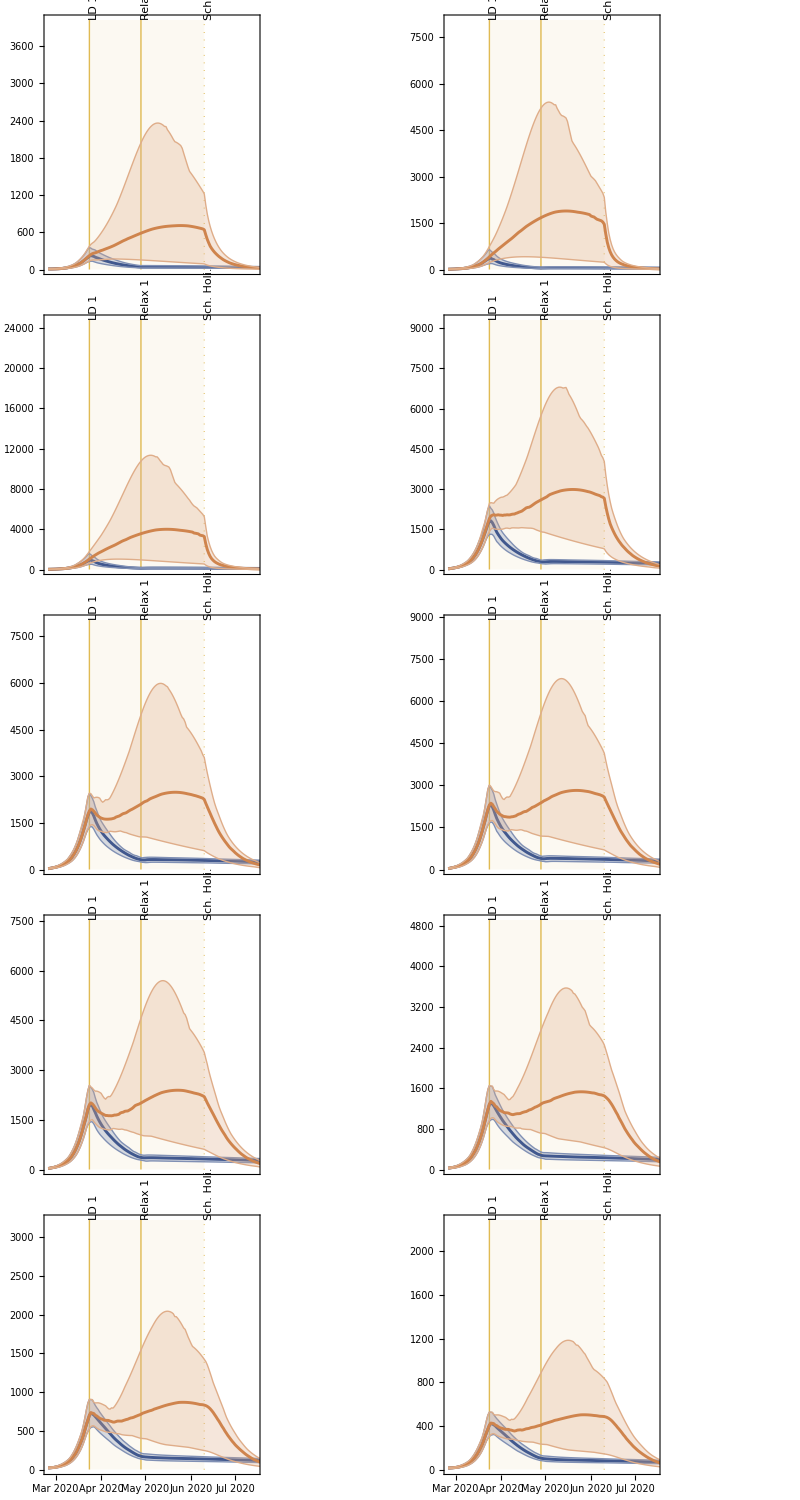
Incidences (1/day) | -Graphics-
 | Dates

```mathematica
figInf10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[incidencesScenarios[[2, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[incidencesScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[incidencesScenarios[[2, k, All, All]],colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figInf10Scen1 = Grid[{{Style[Rotate["Incidences (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figInf10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figInf10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/INCIDENCES_10_SCEN1",  exportFormat[[i]]],figInf10Scen1], {i, 1, Length[exportFormat]}]];
```

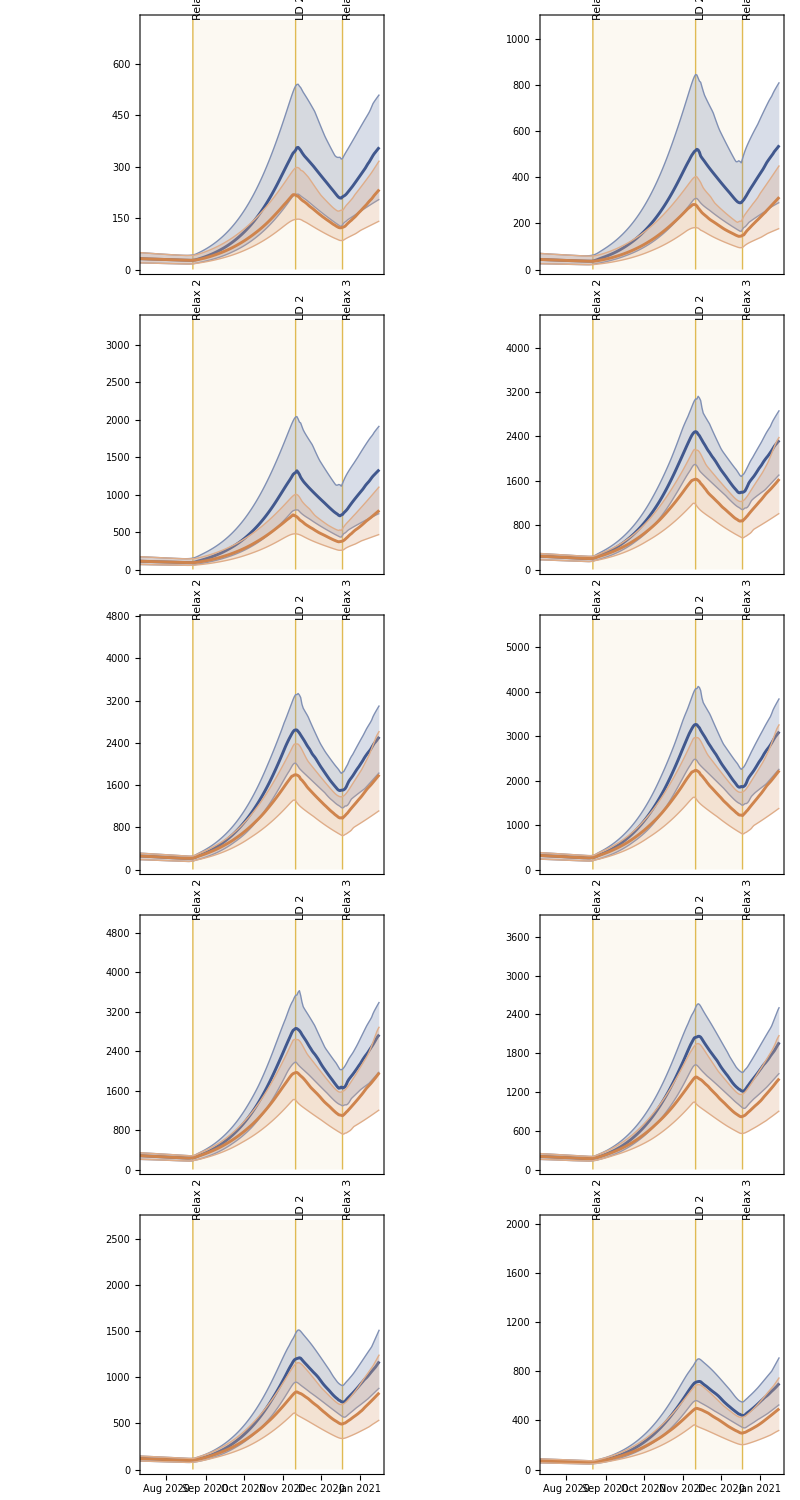
Incidences (1/day) | -Graphics-
 | Dates

```mathematica
figInf10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[incidencesScenarios[[1, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[incidencesScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[incidencesScenarios[[3, k, All, All]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figInf10Scen2 = Grid[{{Style[Rotate["Incidences (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figInf10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figInf10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/INCIDENCES_10_SCEN2",  exportFormat[[i]]],figInf10Scen2], {i, 1, Length[exportFormat]}]];
```